```mathematica
5.00*1.0250/93.127*135.163
```

7.43834

```mathematica
2.50/7.44
```

0.336022

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/Gaussian/3rd-pack"];
```

```mathematica
FileNames[]
```

{acetylannilinepossiblebyproduct2.chk,acetylannilinepossiblebyproduct2.com,acetylannilinepossiblebyproduct2.log,acetylannilinepossiblebyproduct2_uvvis.txt,acetylannilinepossiblebyproduct.chk,acetylannilinepossiblebyproduct.com,acetylannilinepossiblebyproduct.log,aspirinexcitedoptfreq2ndtry.chk,aspirinexcitedoptfreq2ndtry.com,aspirinexcitedoptfreq2ndtry.fchk,aspirinexcitedoptfreq2ndtry.log,aspirinexcitedoptfreq2ndtry_uvvis.txt,aspirinexcitedoptfreq.com,aspirinexcitedoptfreq.fchk,aspirinexcitedoptfreqhf.chk,aspirinexcitedoptfreqhf.com,aspirinexcitedoptfreqhf.fchk,aspirinexcitedoptfreqhf.log,aspirinexcitedoptfreqhf_uvvis.txt,aspirinexcitedoptfreq.log,aspirinexcitedoptfreq_uvvis.txt,benzoicacidDFTLanL2DZ.chk,benzoicacidDFTLanL2DZ.fchk,PBS,sorbictddft.chk,sorbictddft.com,sorbictddft.fchk,sorbictddft.log,sorbictdft2ndtry.chk,sorbictdft2ndtry.com,sorbictdft2ndtry.fchk,sorbictdft2ndtry.log,sorbictdftbvp86.chk,sorbictdftbvp86.com,sorbictdftbvp86.fchk,sorbictdftbvp86.log,sorbictdftbyp86.chk,sorbictdftccpvdz.chk,sorbictdftccpvdz.com,sorbictdftccpvdz.fchk,sorbictdftccpvdz.log,sorbictdhf.chk,sorbictdtdftccpvdz.chk,sorbicthf.chk,sorbicthf.com,sorbicthf.fchk,sorbicthf.log,Walter-Feng.o1017611}

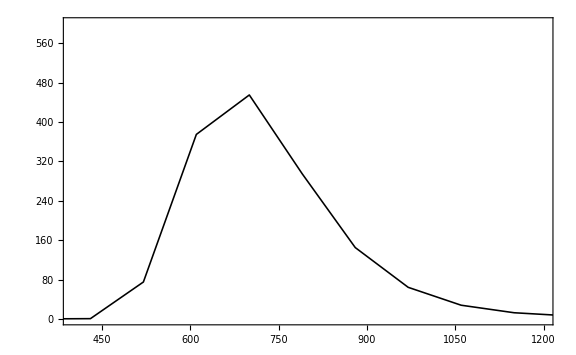

```mathematica
ListLinePlot[{#1,#2}&@@@(Cases[Import["acetylannilinepossiblebyproduct2_uvvis.txt","Table"],{_Real,_Real,_Real}]),PlotRange->{{400,1200},{0,600}},Frame->True,PlotStyle->{Black,Thickness[0.002]},ImageSize->Large,Axes->False]
```

```mathematica
Export["/Users/Apple/Documents/GitHub/LaTeX-Files/基础化学实验报告/figures/byproductuv.eps",%]
```

/Users/Apple/Documents/GitHub/LaTeX-Files/基础化学实验报告/figures/byproductuv.eps

```mathematica
{#1,#2}&@@@(Cases[Import["acetylannilinepossiblebyproduct2_uvvis.txt","Table"],{_Real,_Real,_Real}])
```

{{-20000.,28.7821},{-19910.,28.7554},{-19820.,28.7285},{-19730.,28.7014},{-19640.,28.6739},{-19550.,28.6463},{-19460.,28.6184},{-19370.,28.5902},{-19280.,28.5617},{-19190.,28.533},{-19100.,28.504},{-19010.,28.4747},{-18920.,28.4452},{-18830.,28.4153},{-18740.,28.3852},{-18650.,28.3548},{-18560.,28.3241},{-18470.,28.293},{-18380.,28.2617},{-18290.,28.23},{-18200.,28.1981},{-18110.,28.1658},{-18020.,28.1332},{-17930.,28.1002},{-17840.,28.067},{-17750.,28.0333},{-17660.,27.9994},{-17570.,27.9651},{-17480.,27.9304},{-17390.,27.8954},{-17300.,27.86},{-17210.,27.8242},{-17120.,27.788},{-17030.,27.7515},{-16940.,27.7146},{-16850.,27.6772},{-16760.,27.6395},{-16670.,27.6014},{-16580.,27.5628},{-16490.,27.5238},{-16400.,27.4844},{-16310.,27.4446},{-16220.,27.4043},{-16130.,27.3635},{-16040.,27.3223},{-15950.,27.2807},{-15860.,27.2385},{-15770.,27.1959},{-15680.,27.1528},{-15590.,27.1092},{-15500.,27.0651},{-15410.,27.0204},{-15320.,26.9753},{-15230.,26.9296},{-15140.,26.8833},{-15050.,26.8366},{-14960.,26.7892},{-14870.,26.7413},{-14780.,26.6928},{-14690.,26.6437},{-14600.,26.594},{-14510.,26.5437},{-14420.,26.4927},{-14330.,26.4412},{-14240.,26.389},{-14150.,26.3361},{-14060.,26.2825},{-13970.,26.2283},{-13880.,26.1734},{-13790.,26.1177},{-13700.,26.0614},{-13610.,26.0043},{-13520.,25.9464},{-13430.,25.8878},{-13340.,25.8284},{-13250.,25.7682},{-13160.,25.7072},{-13070.,25.6454},{-12980.,25.5827},{-12890.,25.5191},{-12800.,25.4547},{-12710.,25.3894},{-12620.,25.3232},{-12530.,25.2561},{-12440.,25.188},{-12350.,25.1189},{-12260.,25.0488},{-12170.,24.9778},{-12080.,24.9057},{-11990.,24.8325},{-11900.,24.7583},{-11810.,24.683},{-11720.,24.6065},{-11630.,24.5289},{-11540.,24.4502},{-11450.,24.3702},{-11360.,24.289},{-11270.,24.2066},{-11180.,24.1229},{-11090.,24.0379},{-11000.,23.9516},{-10910.,23.8639},{-10820.,23.7748},{-10730.,23.6843},{-10640.,23.5923},{-10550.,23.4989},{-10460.,23.4039},{-10370.,23.3073},{-10280.,23.2092},{-10190.,23.1094},{-10100.,23.008},{-10010.,22.9048},{-9920.,22.7999},{-9830.,22.6932},{-9740.,22.5846},{-9650.,22.4742},{-9560.,22.3618},{-9470.,22.2475},{-9380.,22.1311},{-9290.,22.0127},{-9200.,21.8921},{-9110.,21.7694},{-9020.,21.6444},{-8930.,21.5171},{-8840.,21.3875},{-8750.,21.2555},{-8660.,21.121},{-8570.,20.9839},{-8480.,20.8443},{-8390.,20.702},{-8300.,20.5569},{-8210.,20.4091},{-8120.,20.2584},{-8030.,20.1047},{-7940.,19.948},{-7850.,19.7882},{-7760.,19.6251},{-7670.,19.4588},{-7580.,19.2892},{-7490.,19.116},{-7400.,18.9394},{-7310.,18.759},{-7220.,18.575},{-7130.,18.3871},{-7040.,18.1952},{-6950.,17.9994},{-6860.,17.7993},{-6770.,17.595},{-6680.,17.3864},{-6590.,17.1732},{-6500.,16.9555},{-6410.,16.733},{-6320.,16.5057},{-6230.,16.2735},{-6140.,16.0361},{-6050.,15.7936},{-5960.,15.5457},{-5870.,15.2924},{-5780.,15.0336},{-5690.,14.769},{-5600.,14.4986},{-5510.,14.2223},{-5420.,13.94},{-5330.,13.6515},{-5240.,13.3568},{-5150.,13.0557},{-5060.,12.7482},{-4970.,12.4341},{-4880.,12.1135},{-4790.,11.7863},{-4700.,11.4525},{-4610.,11.112},{-4520.,10.7649},{-4430.,10.4113},{-4340.,10.0512},{-4250.,9.68471},{-4160.,9.31208},{-4070.,8.93352},{-3980.,8.54931},{-3890.,8.15982},{-3800.,7.76547},{-3710.,7.36681},{-3620.,6.96446},{-3530.,6.55915},{-3440.,6.15173},{-3350.,5.74322},{-3260.,5.33474},{-3170.,4.92761},{-3080.,4.52329},{-2990.,4.12344},{-2900.,3.7299},{-2810.,3.3447},{-2720.,2.97004},{-2630.,2.6083},{-2540.,2.262},{-2450.,1.93372},{-2360.,1.62612},{-2270.,1.34176},{-2180.,1.08305},{-2090.,0.852091},{-2000.,0.650485},{-1910.,0.479188},{-1820.,0.338302},{-1730.,0.22692},{-1640.,0.143029},{-1550.,0.0835177},{-1460.,0.0443457},{-1370.,0.0208875},{-1280.,0.00843941},{-1190.,0.00279243},{-1100.,0.000708557},{-1010.,0.000125311},{-920.,0.0000133816},{-830.,6.898×10^-7},{-740.,1.19×10^-8},{-650.,0.},{-560.,0.},{-470.,0.},{-380.,0.},{-290.,0.},{-200.,0.},{-110.,0.},{-20.,0.},{70.,0.},{160.,0.},{250.,0.},{340.,6.869×10^-7},{430.,0.538571},{520.,75.0212},{610.,374.939},{700.,455.094},{790.,294.707},{880.,145.021},{970.,64.1889},{1060.,27.8441},{1150.,12.546},{1240.,6.38438},{1330.,4.23873},{1420.,3.99638},{1510.,4.76164},{1600.,6.11961},{1690.,7.84848},{1780.,9.80941},{1870.,11.9045},{1960.,14.0607},{2050.,16.2222},{2140.,18.3473},{2230.,20.4056},{2320.,22.3759},{2410.,24.2442},{2500.,26.0024},{2590.,27.6469},{2680.,29.1773},{2770.,30.5955},{2860.,31.9053},{2950.,33.1115},{3040.,34.2196},{3130.,35.2355},{3220.,36.1652},{3310.,37.0148},{3400.,37.79},{3490.,38.4965},{3580.,39.1396},{3670.,39.7244},{3760.,40.2556},{3850.,40.7375},{3940.,41.1743},{4030.,41.5697},{4120.,41.9271},{4210.,42.2498},{4300.,42.5407},{4390.,42.8024},{4480.,43.0374},{4570.,43.248},{4660.,43.4363},{4750.,43.604},{4840.,43.753},{4930.,43.8848},{5020.,44.0008},{5110.,44.1024},{5200.,44.1909},{5290.,44.2672},{5380.,44.3324},{5470.,44.3874},{5560.,44.4331},{5650.,44.4703},{5740.,44.4997},{5830.,44.5218},{5920.,44.5374},{6010.,44.547},{6100.,44.5511},{6190.,44.5501},{6280.,44.5445},{6370.,44.5346},{6460.,44.5209},{6550.,44.5036},{6640.,44.4831},{6730.,44.4596},{6820.,44.4334},{6910.,44.4048},{7000.,44.3739},{7090.,44.341},{7180.,44.3063},{7270.,44.2699},{7360.,44.2319},{7450.,44.1926},{7540.,44.1521},{7630.,44.1105},{7720.,44.0678},{7810.,44.0243},{7900.,43.98},{7990.,43.935},{8080.,43.8894},{8170.,43.8432},{8260.,43.7966},{8350.,43.7496},{8440.,43.7023},{8530.,43.6547},{8620.,43.6068},{8710.,43.5588},{8800.,43.5107},{8890.,43.4625},{8980.,43.4142},{9070.,43.3659},{9160.,43.3176},{9250.,43.2693},{9340.,43.2212},{9430.,43.1731},{9520.,43.1251},{9610.,43.0773},{9700.,43.0297},{9790.,42.9822},{9880.,42.9349},{9970.,42.8878},{10060.,42.841},{10150.,42.7944},{10240.,42.748},{10330.,42.7019},{10420.,42.6561},{10510.,42.6105},{10600.,42.5652},{10690.,42.5202},{10780.,42.4755},{10870.,42.4311},{10960.,42.387},{11050.,42.3432},{11140.,42.2998},{11230.,42.2566},{11320.,42.2138},{11410.,42.1713},{11500.,42.1291},{11590.,42.0872},{11680.,42.0457},{11770.,42.0045},{11860.,41.9636},{11950.,41.923},{12040.,41.8828},{12130.,41.8429},{12220.,41.8033},{12310.,41.7641},{12400.,41.7252},{12490.,41.6866},{12580.,41.6483},{12670.,41.6103},{12760.,41.5727},{12850.,41.5354},{12940.,41.4984},{13030.,41.4617},{13120.,41.4253},{13210.,41.3893},{13300.,41.3535},{13390.,41.3181},{13480.,41.2829},{13570.,41.2481},{13660.,41.2135},{13750.,41.1793},{13840.,41.1454},{13930.,41.1117},{14020.,41.0783},{14110.,41.0453},{14200.,41.0125},{14290.,40.98},{14380.,40.9477},{14470.,40.9158},{14560.,40.8841},{14650.,40.8527},{14740.,40.8216},{14830.,40.7907},{14920.,40.7601},{15010.,40.7298},{15100.,40.6997},{15190.,40.6699},{15280.,40.6403},{15370.,40.611},{15460.,40.5819},{15550.,40.5531},{15640.,40.5245},{15730.,40.4962},{15820.,40.4681},{15910.,40.4403},{16000.,40.4126},{16090.,40.3853},{16180.,40.3581},{16270.,40.3312},{16360.,40.3045},{16450.,40.278},{16540.,40.2517},{16630.,40.2257},{16720.,40.1998},{16810.,40.1742},{16900.,40.1488},{16990.,40.1236},{17080.,40.0986},{17170.,40.0739},{17260.,40.0493},{17350.,40.0249},{17440.,40.0007},{17530.,39.9767},{17620.,39.9529},{17710.,39.9293},{17800.,39.9059},{17890.,39.8827},{17980.,39.8596},{18070.,39.8368},{18160.,39.8141},{18250.,39.7916},{18340.,39.7693},{18430.,39.7471},{18520.,39.7252},{18610.,39.7034},{18700.,39.6817},{18790.,39.6603},{18880.,39.639},{18970.,39.6179},{19060.,39.5969},{19150.,39.5761},{19240.,39.5555},{19330.,39.535},{19420.,39.5147},{19510.,39.4945},{19600.,39.4745},{19690.,39.4546},{19780.,39.4349},{19870.,39.4153},{19960.,39.3959},{20050.,39.3766},{20140.,39.3575},{20230.,39.3385},{20320.,39.3196},{20410.,39.3009},{20500.,39.2824},{20590.,39.2639},{20680.,39.2456},{20770.,39.2275},{20860.,39.2094},{20950.,39.1915},{21040.,39.1738},{21130.,39.1561},{21220.,39.1386},{21310.,39.1212},{21400.,39.1039},{21490.,39.0868},{21580.,39.0698},{21670.,39.0529},{21760.,39.0361},{21850.,39.0194},{21940.,39.0029},{22030.,38.9864},{22120.,38.9701},{22210.,38.9539},{22300.,38.9378},{22390.,38.9219},{22480.,38.906},{22570.,38.8902},{22660.,38.8746},{22750.,38.859},{22840.,38.8436},{22930.,38.8283},{23020.,38.8131},{23110.,38.7979},{23200.,38.7829},{23290.,38.768},{23380.,38.7532},{23470.,38.7384},{23560.,38.7238},{23650.,38.7093},{23740.,38.6949},{23830.,38.6805},{23920.,38.6663},{24010.,38.6521},{24100.,38.6381},{24190.,38.6241},{24280.,38.6103},{24370.,38.5965},{24460.,38.5828},{24550.,38.5692},{24640.,38.5557},{24730.,38.5422},{24820.,38.5289},{24910.,38.5156}}

```mathematica
"/Users/Apple/Documents/NMR.eps"~Export~-Graphics-
```

/Users/Apple/Documents/NMR.eps